Adler et al., iScience, 2020

The Model:

```mathematica
admodel[{ω_,θ_,α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_,I0_,T_,αe_,ϵ_,c_,a_,b_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]==(1-1/2 ω (1+ω)+ω c12[t]/(1+c12[t])) x2[t]+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 (1-1/2 θ (1+θ)+θ c21[t]/(1+c21[t])) x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==I0( UnitStep[t]UnitStep[T-t])+μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1),
e'[t]==x1[t]-αe(ϵ+c x2[t])/(a x2[t]+b x1[t]+1)e[t] };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==(1-1/2 ω (1+ω)+(ω c12[0])/(1+c12[0])) x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 (1-1/2 θ (1+θ)+(θ c21[0])/(1+c21[0])) x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20,e[0]==0}],{x1[t],x2[t],e[t]},{t,0,500}]]
```

Estimating the separatrix:

```mathematica
separatrix[{ω_,θ_,α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]== x2[t](1-1/2 ω (1+ω)+ω c12[t]/(1+c12[t]))+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 (1-1/2 θ (1+θ)+θ c21[t]/(1+c21[t]))x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1) };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==(1-1/2 ω (1+ω)+(ω c12[0])/(1+c12[0])) x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 (1-1/2 θ (1+θ)+(θ c21[0])/(1+c21[0])) x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20}],Norm@{x1[500],x2[500]}<10^-4,{t,0,500}]]
```

Finding the fixed points:

```mathematica
{c21+(c21 x1 α21)/(1+c21)==x1 β11+x2 (1+(c12 ω)/(1+c12)-1/2 ω (1+ω)),c12+(c12 x2 α12)/(1+c12)==x1 β12 (1+(c21 θ)/(1+c21)-1/2 θ (1+θ)),0==x1(-1+(c21 (1-x1) λ1)/(1+c21)),0==x2(-1+(c12 λ2)/(1+c12)) μ2}/.Thread[{ω,θ,α21,α12,β12,β11,μ2,λ1,λ2,x1,x2}->{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,x1/10^6,x2/(β21/(γ k21))^-1}]
```

{c21+(c21 x1 α21)/((1+c21) k21 γ)==(x1 β11)/(k21 γ)+(x2 β21)/(k21 γ),c12+(c12 x2 α12)/((1+c12) k12 γ)==(x1 β12)/(k12 γ),0==(x1 (-1+(c21 (1-x1/1000000) λ1)/((1+c21) μ1)))/1000000,0==(x2 β21 (-1+(c12 λ2)/((1+c12) μ2)) μ2)/(k21 γ μ1)}

```mathematica
FP=Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3},Select[NSolve[{c21+(c21 x1 α21)/((1+c21) k21 γ)==(x1 β11)/(k21 γ)+(x2 β21)/(k21 γ),c12+(c12 x2 α12)/((1+c12) k12 γ)==(x1 β12)/(k12 γ),0==(x1 (-1+(c21 (1-x1/1000000) λ1)/((1+c21) μ1)))/1000000,0==(x2 β21 (-1+(c12 λ2)/((1+c12) μ2)) μ2)/(k21 γ μ1)},{c21,c12,x1,x2}],And@@NonNegative[#[[;;,2]]]&]]
```

{{x2→0,c12→25.8291,c21→0.850581,x1→274778.},{x2→628289.,c12→0.6,c21→1.76304,x1→477599.},{x2→0,c12→0,c21→0,x1→0},{x2→3949.3,c12→0.6,c21→0.507108,x1→9344.96},{x2→0,c12→1.28054,c21→0.51043,x1→13622.8}}

```mathematica
Log10[FP[[;;,{4,1},2]]/.(0->1)]
```

{{5.43898,0},{5.67906,5.79816},{0,0},{3.97058,3.59652},{4.13427,0}}

Figure 2A:

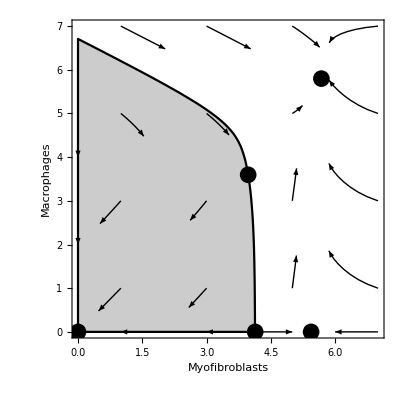

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},
Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]}],Graphics[{Arrowheads[Medium],Arrow[BezierCurve[{#,(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.3),(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.9),
(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->1.2)}]]&/@Flatten[Table[{f0,m0},{f0,{1,3,5,7}},{m0,{1,3,5,7}}],1],
Arrow[{{7,0},{6,0}}],Arrow[{{4.3,0},{5,0}}],Arrow[{{3.9,0},{3,0}}],Arrow[{{2,0},{1,0}}],Arrow[{{0,3},{0,2}}],Arrow[{{0,5},{0,4}}]}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure 2B:

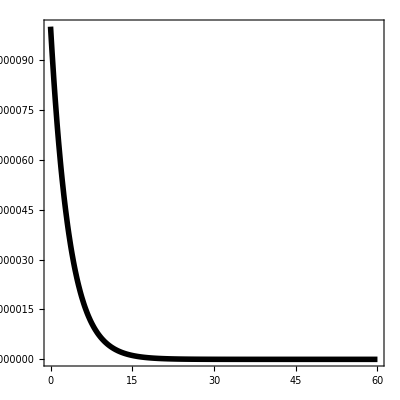
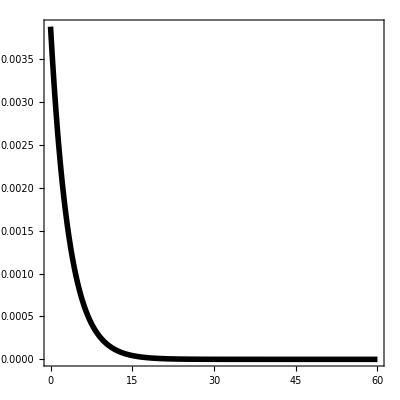
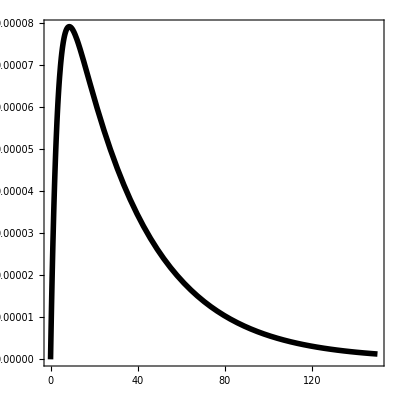
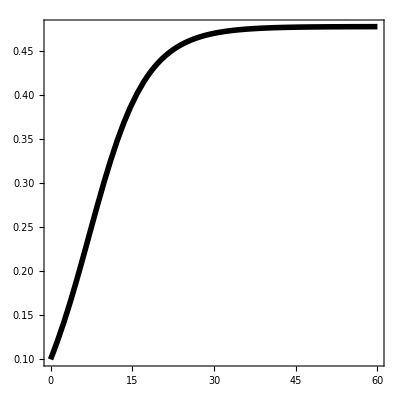
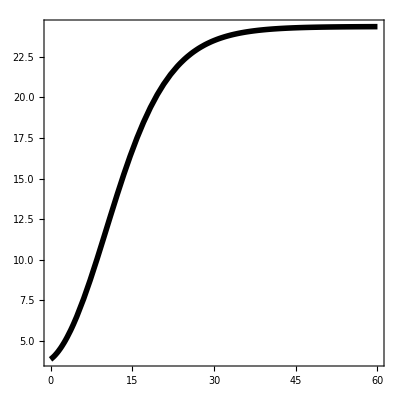
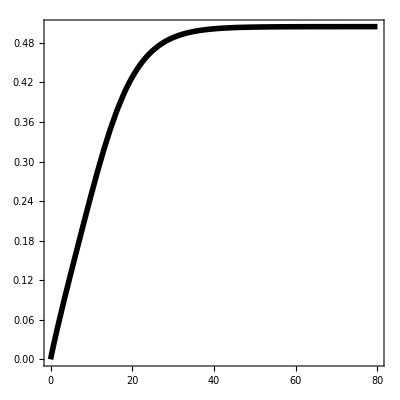
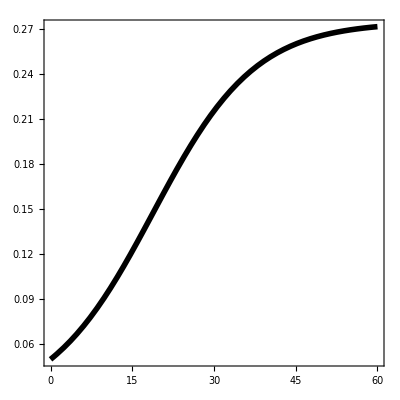
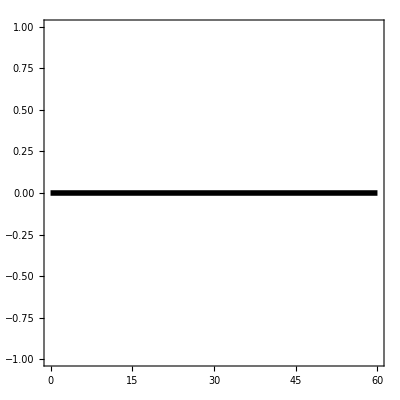

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},Quiet@{{Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^2/10^6,10^2/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,60},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^2/10^6,10^2/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,60},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^2/10^6,10^2/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,150},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True]},{Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^5/10^6,10^5/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,60},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^5/10^6,10^5/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,60},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^5/10^6,10^5/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True]},{Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,(5 10^4)/10^6,0/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,60},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,(5 10^4)/10^6,0/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,60},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,(5 10^4)/10^6,0/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,200},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True]}}]
```

Figure 2C:

Finding the fixed points:

```mathematica
FP2=Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800/100,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3},Select[NSolve[{c21+(c21 x1 α21)/((1+c21) k21 γ)==(x1 β11)/(k21 γ)+(x2 β21)/(k21 γ),c12+(c12 x2 α12)/((1+c12) k12 γ)==(x1 β12)/(k12 γ),0==(x1 (-1+(c21 (1-x1/1000000) λ1)/((1+c21) μ1)))/1000000,0==(x2 β21 (-1+(c12 λ2)/((1+c12) μ2)) μ2)/(k21 γ μ1)},{c21,c12,x1,x2}],And@@NonNegative[#[[;;,2]]]&]]
```

{{x2→0,c12→0,c21→0,x1→0},{x2→0,c12→0.0128054,c21→0.51043,x1→13622.8},{x2→0,c12→0.258291,c21→0.850581,x1→274778.}}

```mathematica
Log10[FP2[[;;,{4,1},2]]/.(0->1)]
```

{{0,0},{4.13427,0},{5.43898,0}}

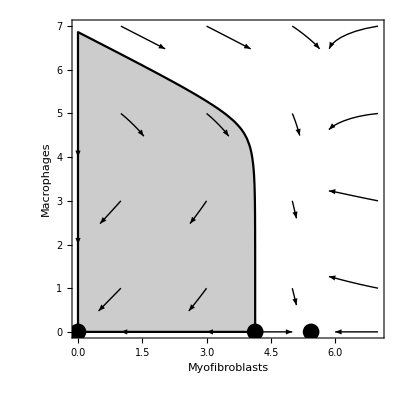

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800/100,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},Quiet@Show[Graphics[{PointSize[0.03],Point[Log10[FP2[[;;,{4,1},2]]/.(0->1)]]}],Graphics[{Arrowheads[Medium],Arrow[BezierCurve[{#,(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.3),(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.9),
(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->1.2)}]]&/@Flatten[Table[{f0,m0},{f0,{1,3,5,7}},{m0,{1,3,5,7}}],1],
Arrow[{{7,0},{6,0}}],Arrow[{{4.3,0},{5,0}}],Arrow[{{3.9,0},{3,0}}],Arrow[{{2,0},{1,0}}],Arrow[{{0,3},{0,2}}],Arrow[{{0,5},{0,4}}]}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure 2D:

Model with CSF down regulation:

Estimating the separatrix:

```mathematica
separatrix2[{ω_,θ_,α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_}]:=Module[{adeq,steq,hf},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]== x2[t](1-1/2 ω (1+ω)+ω c12[t]/(1+c12[t]))+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 (1-1/2 θ (1+θ)+θ c21[t]/(1+c21[t]))x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1) };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==(1-1/2 ω (1+ω)+(ω c12[0])/(1+c12[0])) x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 (1-1/2 θ (1+θ)+(θ c21[0])/(1+c21[0])) x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
hf=Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==.9,x2[0]==20}],{x1[500],x2[500]},{t,0,500}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20}],Norm[{x1[500],x2[500]}-hf]<10^-5,{t,0,500}]]
```

```mathematica
pnts4=Table[Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=279.13846153846157(*1353600*),α21=39000.(*734400*),β11=11440(*345600*),β12=2520.(*676800*),β21=100800,γ=2,λ1=2.4(*0.9*),λ2=2.4(*0.8*),μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,10^5.4/(10^(Log10@((β21/(γ k21))^-1))),0,0,1,1,1,1,1}]⟦1;;2⟧)]/.t->T)],{T,0,2,1}]
```

{{8.88178×10^-16,5.4},{2.52423,4.96572},{4.42807,4.53467}}

Finding the fixed points:

```mathematica
FP3=Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=279.13846153846157(*1353600*),α21=39000.(*734400*),β11=11440(*345600*),β12=2520.(*676800*),β21=100800,γ=2,λ1=2.4(*0.9*),λ2=2.4(*0.8*),μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},Select[NSolve[{c21+(c21 x1 α21)/((1+c21) k21 γ)==(x1 β11)/(k21 γ)+(x2 β21)/(k21 γ),c12+(c12 x2 α12)/((1+c12) k12 γ)==((1-c21/(1+c21)) x1 β12)/(k12 γ),0==(x1 (-1+(c21 (1-x1/1000000) λ1)/((1+c21) μ1)))/1000000,0==(x2 β21 (-1+(c12 λ2)/((1+c12) μ2)) μ2)/(k21 γ μ1)},{c21,c12,x1,x2}],And@@NonNegative[Re@#[[{1,4},2]]]&]]
```

{{x2→0,c12→0,c21→0,x1→0},{x2→0,c12→0.0195153,c21→0.154198,x1→64355.7},{x2→0,c12→-0.0317925,c21→-10.7607,x1→886616.},{x2→12561.9,c12→0.142857,c21→0.428592,x1→583347.},{x2→51088.+2.0807×10^-9 ⅈ,c12→0.142857,c21→0.708597,x1→698595.+5.34347×10^-9 ⅈ}}

```mathematica
Log10[Re[FP3[[;;,{4,1},2]]]/.(0->1)]
```

{{0,0},{4.80859,0},{5.94774,0},{5.76593,4.09905},{5.84423,4.70832}}

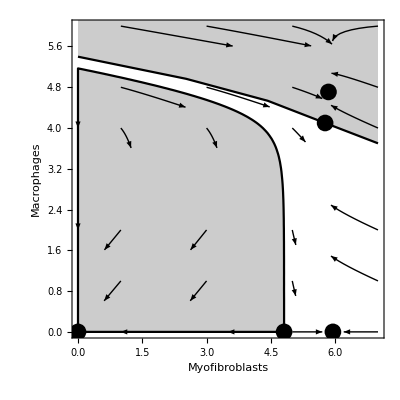

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=279.13846153846157(*1353600*),α21=39000.(*734400*),β11=11440(*345600*),β12=2520.(*676800*),β21=100800,γ=2,λ1=2.4(*0.9*),λ2=2.4(*0.8*),μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},Quiet@Show[
ListLinePlot[Join[pnts4,Log10[Re[FP3[[;;,{4,1},2]]]/.(0->1)][[{4}]],{{7,3.7}}],InterpolationOrder->1,Filling->7,PlotStyle->Black],
Graphics[{PointSize[0.03],Point[Log10[FP3[[;;,{4,1},2]]/.(0->1)]]}],Graphics[{Arrowheads[Medium],Arrow[BezierCurve[{#,(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.3),(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(#[[1]])/10^6,10^(#[[2]])/(10^(Log10@((β21/(γ k21))^-1))),0,τ1,1,1,1,1,1}]⟦1;;2⟧)]/.t->0.9)}]]&/@Flatten[Table[{f0,m0},{f0,{1,3,5,7}},{m0,{1,2,4,4.8,6}}],1],
Arrow[{{7,0},{6.2,0}}],Arrow[{{5,0},{5.7,0}}],Arrow[{{4.5,0},{3.5,0}}],Arrow[{{2,0},{1,0}}],Arrow[{{0,3},{0,2}}],Arrow[{{0,5},{0,4}}]}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,6}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure 3:

Figure 3B:

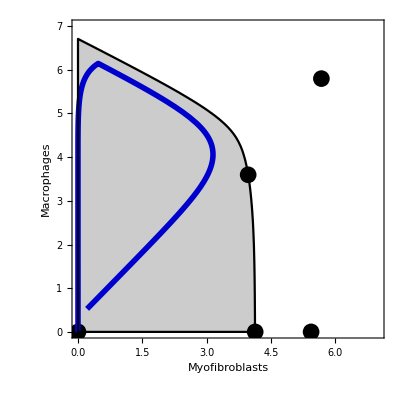

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6},Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,47},PlotStyle->{Thickness[0.01],Blue}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure 3D:

Model repetitive injury:

```mathematica
admodelRepet[{ω_,θ_,α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_,I0_,T_,αe_,ϵ_,c_,a_,b_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]==(1-1/2 ω (1+ω)+ω c12[t]/(1+c12[t])) x2[t]+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 (1-1/2 θ (1+θ)+θ c21[t]/(1+c21[t])) x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==I0( UnitStep[t]UnitStep[T-t]+UnitStep[t-T-2]UnitStep[2T+2-t])+μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1),
e'[t]==x1[t]-αe(ϵ+c x2[t])/(a x2[t]+b x1[t]+1)e[t] };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==(1-1/2 ω (1+ω)+(ω c12[0])/(1+c12[0])) x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 (1-1/2 θ (1+θ)+(θ c21[0])/(1+c21[0])) x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20,e[0]==0}],{x1[t],x2[t],e[t]},{t,0,500}]]
```

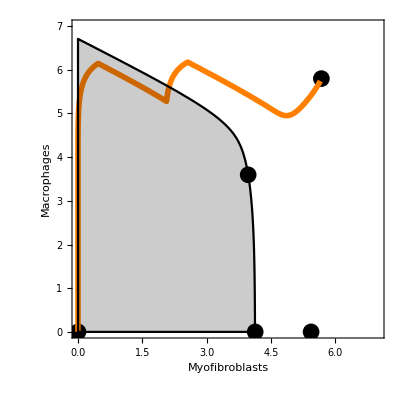

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,47},PlotStyle->{Thickness[0.01],Orange}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure 3F:

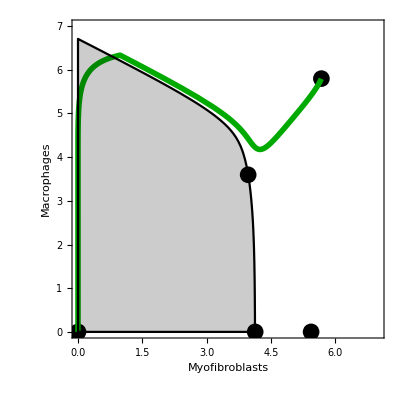

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=1.2},Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker[Green]}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure 3G:

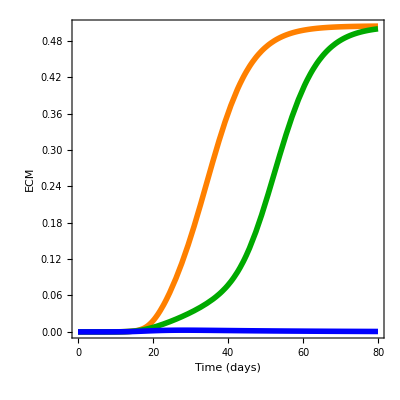

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},
Quiet@Show[
Plot[(Evaluate[admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker@Green},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Blue},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],FrameLabel->{"Time (days)","ECM"}]]
```

Figure 3H:

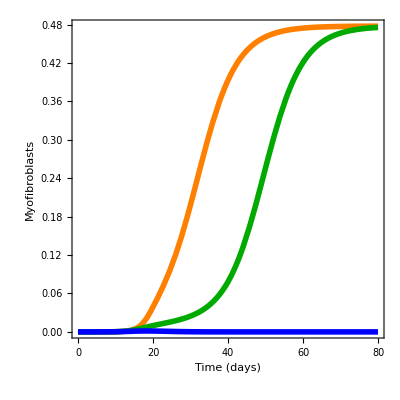

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},
Quiet@Show[
Plot[(Evaluate[admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker@Green},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Blue},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],FrameLabel->{"Time (days)","Myofibroblasts"}]]
```

Figure 3I:

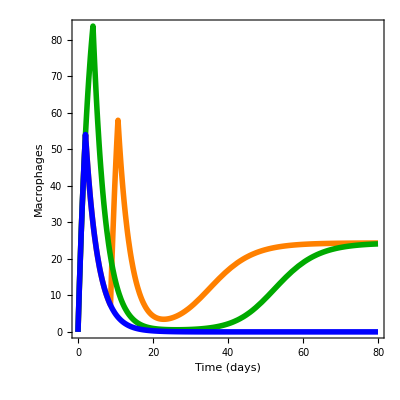

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.2},
Quiet@Show[
Plot[(Evaluate[admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker@Green},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Blue},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],FrameLabel->{"Time (days)","Macrophages"}]]
```

Figure 3J:

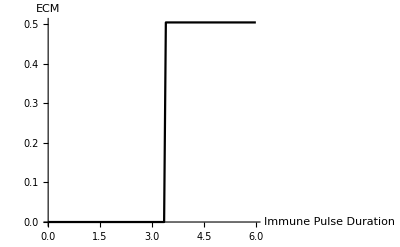

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3},ListLinePlot[Table[{τ,admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,0.3τ,α,ϵ,c,a,b}][[3]]/.t->100},{τ,0,6,.05}],PlotStyle->Black,AxesLabel->{"Immune Pulse Duration","ECM"}]]
```

Figure 4:

Figure 4A:

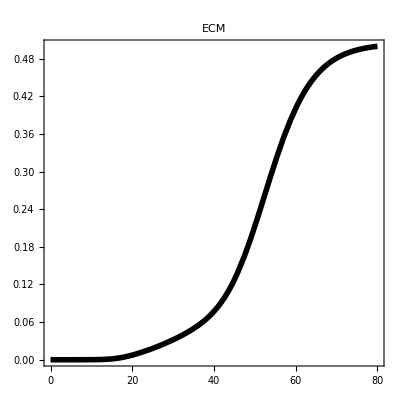

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=1.2},Quiet@Show[Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],PlotLabel->"ECM"]]
```

Figure 4B:

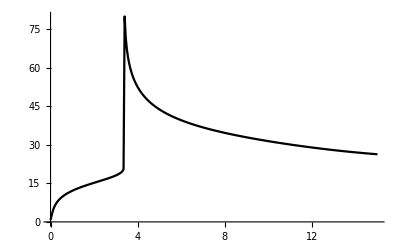

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,max,tmax,s},
ListLinePlot[
Table[
{τ,
s=admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,0.3 τ,1,1,1,1,1}];
{max,tmax}={#[[1]],#[[2,1,2]]}&@NMaximize[{s[[3]],0<t<100},t];
1/0.3 FindRoot[Evaluate[s[[3]]==max/2],{t,0,0,tmax}][[1,2]]},
{τ,0,15,.05}],
PlotRange->All,PlotStyle->Black]]
```

Figure 4C:

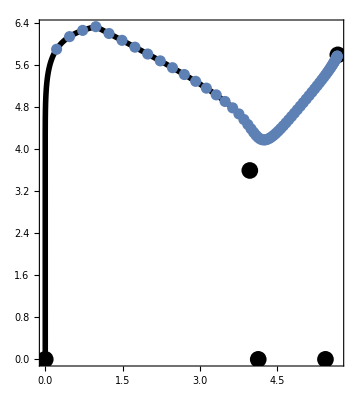
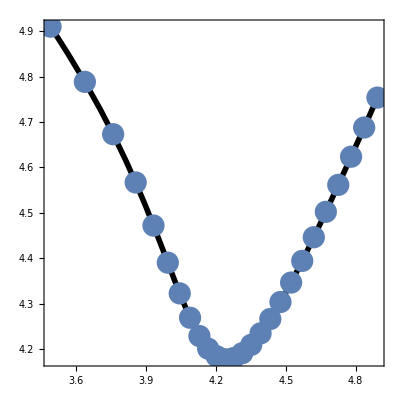

```mathematica
Module[{k=10^6,a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ2=1.2},
{Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]},Frame->True],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)]),{t,0,20},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
ListPlot[Table[Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1],{t1,1,70,1}],PlotStyle->PointSize[0.02]]],Quiet@Show[
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)]),{t,15 0.3,40 0.3},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
ListPlot[Table[Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1],{t1,15,40,1}],PlotStyle->PointSize[0.04]]]}]
```

Figure 4D:

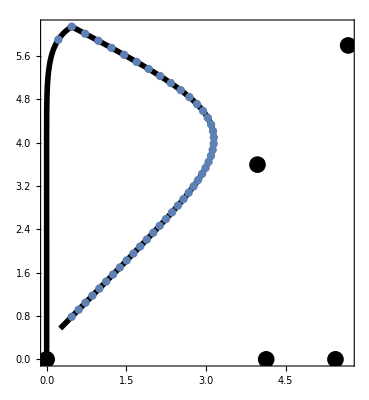
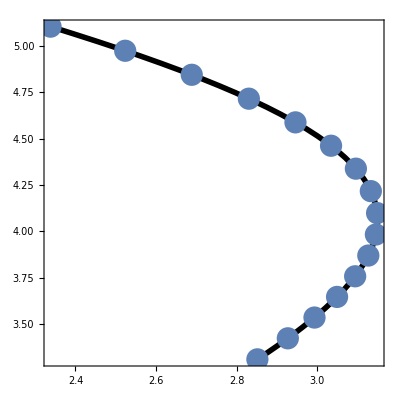

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6},
{Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]},Frame->True],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)]),{t,0,14},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
ListPlot[Table[Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1],{t1,1,45,1}],PlotStyle->PointSize[0.015]]],Quiet@Show[
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)]),{t,10 0.3,25 0.3},PlotStyle->{Thickness[0.01],Black},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
ListPlot[Table[Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1],{t1,10,25,1}],PlotStyle->PointSize[0.04]]]}]
```

Figure 5:

Figure 5A:

```mathematica
CriticalTimeNormParams[{α21_,α12_,β12_,β11_,λ1_,λ2_}]:=MaximalBy[{(#[[1,1]]+#[[2,1]])/2,(#[[2,2]]-#[[1,2]])/(#[[2,1]]-#[[1,1]])}&/@Partition[Table[{τ,Evaluate@(admodel[{0,0,α21,α12,β12,β11,1,λ1,λ2,1/10^6,1/10^4,120,0.3τ,.1,1,1,1,1}][[3]])/.t->50},{τ,0,40,.05}],2,1],Last][[1,1]];
```

```mathematica
tbbeta11=Table[{β11,CriticalTimeNormParams[{282,4.8,94,β11 132,3,2.7}]},{β11,.5,1,.01}];
tbalpha21=Table[{α21,CriticalTimeNormParams[{α21 282,4.8,94, 132,3,2.7}]},{α21,1,1.7,.01}];
tblambda1=Table[{λ1,CriticalTimeNormParams[{282,4.8,94, 132,λ1 3,2.7}]},{λ1,.5,1,.01}];
tbalpha12=Table[{α12,CriticalTimeNormParams[{282,α12 4.8,94, 132, 3,2.7}]},{α12,1,1.7,.01}];
tbbeta12=Table[{β12,CriticalTimeNormParams[{282, 4.8,β12 94, 132, 3,2.7}]},{β12,.5,1,.01}];
tblambda2=Table[{λ2,CriticalTimeNormParams[{282, 4.8, 94, 132, 3,λ2 2.7}]},{λ2,.5,1,.01}];
```

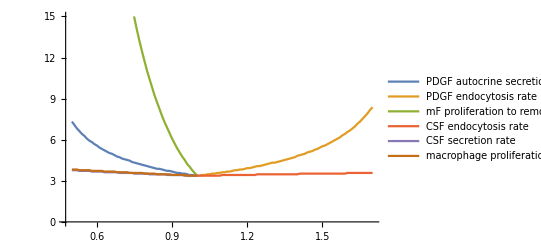

```mathematica
ListLinePlot[{tbbeta11,tbalpha21,tblambda1,tbalpha12,tbbeta12,tblambda2},PlotLegends->{"PDGF autocrine secretion rate","PDGF endocytosis rate","mF proliferation to removal rate","CSF endocytosis rate","CSF secretion rate","macrophage proliferation to removal rate"},PlotRange->{All,{0,15}}]
```

Figure 5B:

Finding the fixed points:

```mathematica
FPM1=Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21M1=734400 1.2,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3},Select[NSolve[{c21+(c21 x1 α21M1)/((1+c21) k21 γ)==(x1 β11)/(k21 γ)+(x2 β21)/(k21 γ),c12+(c12 x2 α12)/((1+c12) k12 γ)==(x1 β12)/(k12 γ),0==(x1 (-1+(c21 (1-x1/1000000) λ1)/((1+c21) μ1)))/1000000,0==(x2 β21 (-1+(c12 λ2)/((1+c12) μ2)) μ2)/(k21 γ μ1)},{c21,c12,x1,x2}],And@@NonNegative[#[[;;,2]]]&]]
```

{{x2→491086.,c12→0.6,c21→1.14167,x1→374697.},{x2→0,c12→10.8123,c21→0.604257,x1→115025.},{x2→0,c12→0,c21→0,x1→0},{x2→7411.32,c12→0.6,c21→0.509119,x1→11941.5},{x2→0,c12→3.06304,c21→0.525695,x1→32585.5}}

```mathematica
Log10[FPM1[[;;,{4,1},2]]/.(0->1)]
```

{{5.57368,5.69116},{5.06079,0},{0,0},{4.07706,3.8699},{4.51302,0}}

```mathematica
FPM2=Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21M2=734400 1.5,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3},Select[NSolve[{c21+(c21 x1 α21M2)/((1+c21) k21 γ)==(x1 β11)/(k21 γ)+(x2 β21)/(k21 γ),c12+(c12 x2 α12)/((1+c12) k12 γ)==(x1 β12)/(k12 γ),0==(x1 (-1+(c21 (1-x1/1000000) λ1)/((1+c21) μ1)))/1000000,0==(x2 β21 (-1+(c12 λ2)/((1+c12) μ2)) μ2)/(k21 γ μ1)},{c21,c12,x1,x2}],And@@NonNegative[#[[;;,2]]]&]]
```

{{x2→0,c12→0,c21→0,x1→0},{x2→276507.,c12→0.6,c21→0.735992,x1→213763.},{x2→19443.8,c12→0.6,c21→0.516235,x1→20965.9}}

```mathematica
Log10[FPM2[[;;,{4,1},2]]/.(0->1)]
```

{{0,0},{5.32993,5.44171},{4.32151,4.28878}}

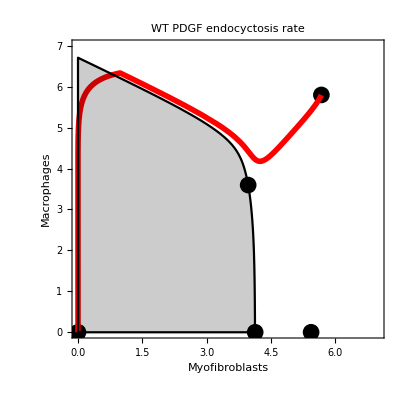
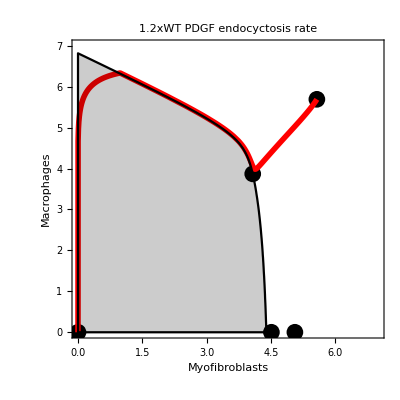
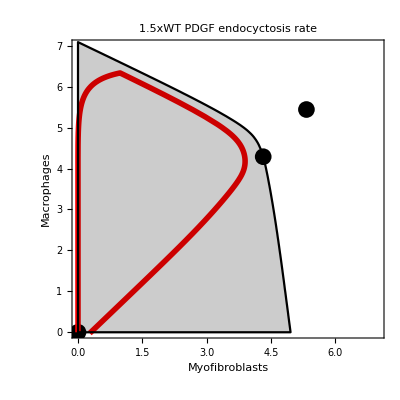

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21M2=734400 1.5,α21M1=734400 1.2,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ2=4 0.3},
{Show[
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]}],ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)]),{t,0,25},PlotStyle->{Thickness[0.01],Red}],ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"},PlotLabel->"WT PDGF endocyctosis rate"],
Show[
Graphics[{PointSize[0.03],Point[Log10[FPM1[[;;,{4,1},2]]/.(0->1)]]}],ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21M1 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)]),{t,0,50},PlotStyle->{Thickness[0.01],Red}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21M1 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"},PlotLabel->"1.2xWT PDGF endocyctosis rate"],
Show[
Graphics[{PointSize[0.03],Point[Log10[FPM2[[;;,{4,1},2]]/.(0->1)]]}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21M2 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)]),{t,0,20},PlotStyle->{Thickness[0.01],Red}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21M2 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"},PlotLabel->"1.5xWT PDGF endocyctosis rate"]}]//Quiet
```

Figure 5C-D:

```mathematica
model1[{α21_,α12_,β12_,β11_,μ2_,λ1_,λ2_,x10_,x20_}]:=Module[{adeq,steq},
adeq={
c21[t]+α21 c21[t]/(1+c21[t])x1[t]== x2[t]+β11 x1[t],
c12[t]+α12 c12[t]/(1+c12[t])x2[t]==β12 x1[t],
x1'[t]== x1[t](λ1 c21[t]/(1+c21[t])(1-x1[t])-1) ,
x2'[t]==μ2 x2[t] (λ2 c12[t]/(1+c12[t])-1) };
steq=Equal@@@FindRoot[{c21[0]+(α21 c21[0] x10)/(1+c21[0])==x20+β11 x10,c12[0]+(α12 c12[0])/(1+c12[0])x20==β12 x10},{c12[0],1,0,∞},{c21[0],1,0,∞}];
Quiet@NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20}],Norm@{x1[500],x2[500]}<10^-4,{t,0,500}]]
```

```mathematica
HEAL[x01_?NumericQ,x02_?NumericQ,λ1_,μ1_,α21_,β11_]:=Module[{k12=3.6*^9,k21=1.3*^9,α12=1353600,(*α21=734400,β11=345600,*)β12=676800,β21=100800,γ=2,(*λ1=0.9,*)λ2=0.8,(*μ1=0.3,*)μ2=0.3},
model1[{(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}]]
```

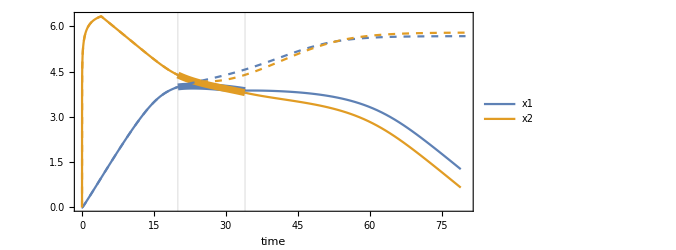
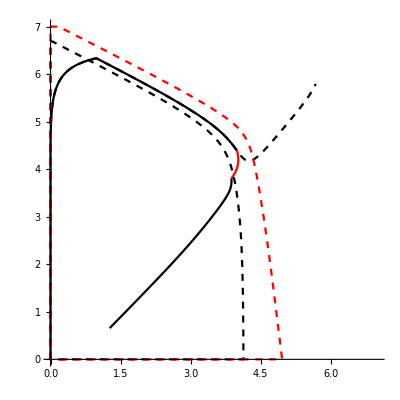
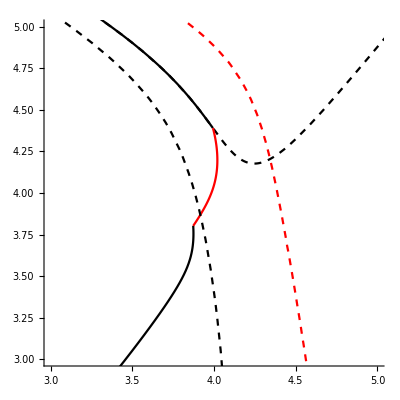

```mathematica
Module[{ic1,ic2,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,t0=20,dur=14,mod},
mod[ic_,α_,I0_,τ_]:=({6,Log10@((β21/(γ k21))^-1)}+Log10@admodel[{0,0,(α 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(-6+ic⟦1⟧),β21/(k21 γ)10^ic⟦2⟧,I0,τ,1,1,1,1,1}][[;;2]]);
ic1=mod[{0,0},α21,120,1.2]/.t->0.3 t0;
ic2=mod[ic1,1.5 α21,0,0]/.t->0.3dur;
{Show[
{
ParametricPlot[Evaluate@Thread[{t1+0t0,mod[{0.,0.},α21,120,1.2]/.t->0.3 t1}],{t1,0, t0},PlotLegends->{"x1","x2"}],
ParametricPlot[Evaluate@Thread[{t1+t0,mod[ic1,1.5 α21,0,0]/.t->0.3 t1}],{t1,0, dur},PlotStyle->Thickness[.01]],
ParametricPlot[Evaluate@Thread[{t1+t0+dur,mod[ic2,α21,0,0]/.t->0.3 t1}],{t1,0, 45}],
ParametricPlot[Evaluate@Thread[{t1+0t0,mod[{0.,0.},α21,120,1.2]/.t->0.3 t1}],{t1,0, 80},PlotStyle->Dashed]},
PlotRange->{{0,All},{0,All}},AspectRatio->.5,Frame->True,Axes->False,PlotRangePadding->.2,GridLines->{{t0,t0+dur},None},ImageSize->500,FrameLabel->{"time",None}],
Show[
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,80},PlotRange->{{0,7},{0,7}},PlotStyle->{Black,Dashed}],
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,t0},PlotRange->{{0,7},{0,7}},PlotStyle->Black],
ParametricPlot[Evaluate@mod[ic1,1.5 α21,0,0]/.t->0.3 t1,{t1,0,dur},PlotRange->{{0,7},{0,7}},PlotStyle->Red],
ParametricPlot[Evaluate@mod[ic2,α21,0,0]/.t->0.3 t1,{t1,0,45},PlotRange->{{0,7},{0,7}},PlotStyle->Black],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL[x01,x02,λ1,μ1,#,β11],{x01,0,6},{x02,0,7}],{{_Real,_Real}..}|Line[y_],∞]&/@{α21,1.5 α21},
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,PlotStyle->{{Black,Dashed},{Red,Dashed}}]],
Show[
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,80},PlotStyle->{Black,Dashed}],
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,t0},PlotStyle->Black],
ParametricPlot[Evaluate@mod[ic1,1.5 α21,0,0]/.t->0.3 t1,{t1,0,dur},PlotStyle->Red],
ParametricPlot[Evaluate@mod[ic2,α21,0,0]/.t->0.3 t1,{t1,0,45},PlotStyle->Black],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL[x01,x02,λ1,μ1,#,β11],{x01,0,6},{x02,0,7}],{{_Real,_Real}..}|Line[y_],∞]&/@{α21,1.5 α21},AspectRatio->1,Axes->False,Frame->True,PlotStyle->{{Black,Dashed},{Red,Dashed}}],PlotRange->{{3,5},{3,5}}]}]//Quiet
```

Figure 5E:

```mathematica
modelDrug[ic_,α21_,I0_,τ_]:=Module[{k12=3.6*^9,k21=1.3*^9,α12=1353600,(*α21=734400,*)β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3},
({6,Log10@((β21/(γ k21))^-1)}+Log10@admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(-6+ic⟦1⟧),β21/(k21 γ)10^ic⟦2⟧,I0,τ,1,1,1,1,1}][[;;2]])]
```

```mathematica
Heal[d_,dur_]:=
Module[{ic1,ic2,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,Δt1=20},
ic1=modelDrug[{0,0},α21,120,1.2]/.t->0.3 Δt1;
ic2=modelDrug[ic1,d α21,0,0]/.t->0.3dur;
And@@Negative[Re[Evaluate@modelDrug[ic2,α21,0,0]/.t->100]]]
```

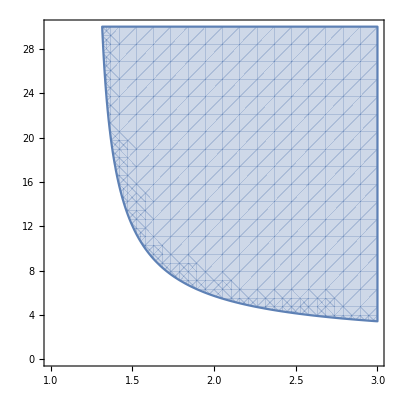

```mathematica
RegionPlot[Heal[d,dur],{d,1,3},{dur,0,30}]//Quiet
```

Figure 5F-G:

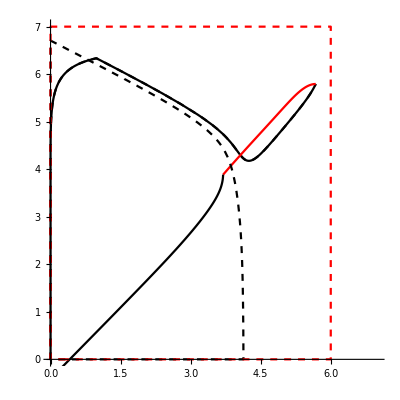
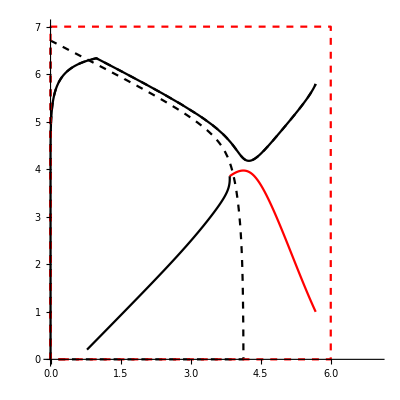

```mathematica
Module[{ic1,ic2,ic3,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,t0=80,dur=40,dur2=25,mod},
mod[ic_,α_,I0_,τ_]:=({6,Log10@((β21/(γ k21))^-1)}+Log10@admodel[{0,0,(α 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(-6+ic⟦1⟧),β21/(k21 γ)10^ic⟦2⟧,I0,τ,1,1,1,1,1}][[;;2]]);
ic1=mod[{0,0},α21,120,1.2]/.t->0.3 t0;
ic2=mod[ic1,3 α21,0,0]/.t->0.3dur;
ic3=mod[{ic1[[1]],1},3α21,0,0]/.t->0.3dur2;
{Show[
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,80},PlotRange->{{0,7},{0,7}},PlotStyle->{Black,Dashed}],
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,t0},PlotRange->{{0,7},{0,7}},PlotStyle->Black],
ParametricPlot[Evaluate@mod[ic1,3 α21,0,0]/.t->0.3 t1,{t1,0,dur},PlotRange->{{0,7},{0,7}},PlotStyle->Red],
ParametricPlot[Evaluate@mod[ic2,α21,0,0]/.t->0.3 t1,{t1,0,45},PlotRange->{{0,7},{0,7}},PlotStyle->Black],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL[x01,x02,λ1,μ1,#,β11],{x01,0,6},{x02,0,7}],{{_Real,_Real}..}|Line[y_],∞]&/@{α21,3 α21},
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,PlotStyle->{{Black,Dashed},{Red,Dashed}}]],
Show[
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,80},PlotRange->{{0,7},{0,7}},PlotStyle->{Black,Dashed}],
ParametricPlot[Evaluate@mod[{0.,0.},α21,120,1.2]/.t->0.3 t1,{t1,0,t0},PlotRange->{{0,7},{0,7}},PlotStyle->Black],ParametricPlot[Evaluate@mod[{ic1[[1]],1},3 α21,0,0]/.t->0.3 t1,{t1,0,dur2},PlotRange->{{0,7},{0,7}},PlotStyle->Red],
ParametricPlot[Evaluate@mod[ic3,α21,0,0]/.t->0.3 t1,{t1,0,45},PlotRange->{{0,7},{0,7}},PlotStyle->Black],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[RegionPlot[HEAL[x01,x02,λ1,μ1,#,β11],{x01,0,6},{x02,0,7}],{{_Real,_Real}..}|Line[y_],∞]&/@{α21,3 α21},
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,PlotStyle->{{Black,Dashed},{Red,Dashed}}]]}]//Quiet
```

Figure S1:

```mathematica
withEpithelium[{α21_,α12_,β21_,β12_,β11_,k12_,k21_,μ1_,μ2_,λ1_,λ2_,k_,γ_,x10_,x20_,T_,d_,α_,hE0_}]:=Module[{adeq,steq},
adeq={
γ c21[t]+α21 c21[t]/(k21+c21[t])x1[t]==β21 x2[t]+β11 x1[t],
γ c12[t]+α12 c12[t]/(k12+c12[t])x2[t]==β12 x1[t],
x1'[t]== x1[t](λ1 c21[t]/(k21+c21[t])(1-x1[t]/k)-μ1) ,
x2'[t]==dE[t]+x2[t] (λ2 c12[t]/(k12+c12[t])-μ2),
dE'[t]==d( UnitStep[t]UnitStep[T-t])(hE[t])-α dE[t],
hE'[t]==-d( UnitStep[t]UnitStep[T-t])(hE[t])+α dE[t]};
steq=Equal@@@FindRoot[{γ c21[0]+(α21 c21[0] x10)/(k21+c21[0])==β21 x20+β11 x10,γ c12[0]+(α12 c12[0])/(k12+c12[0])x20==β12 x10},{c12[0],10^8,0,∞},{c21[0],10^8,0,∞}];
NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20,dE[0]==0,hE[0]==hE0}],{x1[t],x2[t],dE[t]},{t,0,100}]]
```

```mathematica
withEpitheliumRepet[{α21_,α12_,β21_,β12_,β11_,k12_,k21_,μ1_,μ2_,λ1_,λ2_,k_,γ_,x10_,x20_,T_,d_,α_,hE0_}]:=Module[{adeq,steq},
adeq={
γ c21[t]+α21 c21[t]/(k21+c21[t])x1[t]==β21 x2[t]+β11 x1[t],
γ c12[t]+α12 c12[t]/(k12+c12[t])x2[t]==β12 x1[t],
x1'[t]== x1[t](λ1 c21[t]/(k21+c21[t])(1-x1[t]/k)-μ1) ,
x2'[t]==dE[t]+x2[t] (λ2 c12[t]/(k12+c12[t])-μ2),
dE'[t]==d( UnitStep[t]UnitStep[T-t]+UnitStep[t-T-2]UnitStep[2T+2-t])(hE[t])-α dE[t],
hE'[t]==-d( UnitStep[t]UnitStep[T-t]+UnitStep[t-T-2]UnitStep[2T+2-t])(hE[t])+α dE[t]};
steq=Equal@@@FindRoot[{γ c21[0]+(α21 c21[0] x10)/(k21+c21[0])==β21 x20+β11 x10,γ c12[0]+(α12 c12[0])/(k12+c12[0])x20==β12 x10},{c12[0],10^8,0,∞},{c21[0],10^8,0,∞}];
NDSolveValue[Join[adeq,steq,{x1[0]==x10,x2[0]==x20,dE[0]==0,hE[0]==hE0}],{x1[t],x2[t],dE[t]},{t,0,100}]]
```

```mathematica
Show[{
ParametricPlot3D[#[[1]],{t,10^-6,50},PlotStyle->{Thickness[0.01],#[[2]]}],Graphics3D[{PointSize[.05],White,Point[#[[1]]/.t->10^-6],Black,Point[#[[1]]/.t->50]}]}&/@{{Log10@(withEpithelium[{734400,1353600,100800,676800,345600,3.6*^9,1.3*^9,0.3,0.3,0.9,0.8,10^6,2,10^0.1 ,10^0,3,10^2,1,10^6}]⟦1;;3⟧),Darker@Green},{Log10@(withEpithelium[{734400,1353600,100800,676800,345600,3.6*^9,1.3*^9,0.3,0.3,0.9,0.8,10^6,2,10^0 ,10^0,1,10^2,1,10^6}]⟦1;;3⟧),Cyan}},
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"myofibroblasts","macrophages","damaged epitheluim"},
Exclusions->None,
AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

```mathematica
Show[{
ParametricPlot3D[#[[1]],{t,10^-6,50},PlotStyle->{Thickness[0.01],#[[2]]}],Graphics3D[{PointSize[.05],White,Point[#[[1]]/.t->10^-6],Black,Point[#[[1]]/.t->50]}]}&/@{{Log10@(withEpitheliumRepet[{734400,1353600,100800,676800,345600,3.6*^9,1.3*^9,0.3,0.3,0.9,0.8,10^6,2,10^0.1 ,10^0,1,10^2,1,10^6}]⟦1;;3⟧),Orange},{Log10@(withEpithelium[{734400,1353600,100800,676800,345600,3.6*^9,1.3*^9,0.3,0.3,0.9,0.8,10^6,2,10^0 ,10^0,1,10^2,1,10^6}]⟦1;;3⟧),Cyan}},
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"myofibroblasts","macrophages","damaged epitheluim"},
Exclusions->None,
AxesEdge->{{-1,-1},{1,-1},{-1,-1}}]
```

-Graphics3D-

Figure S2:

The reference parameters:

```mathematica
{(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2}/.Thread[{k12,k21,α12,α21,β11,β12,β21,γ,λ1,λ2,μ1,μ2}->{3.6*^9,1.3*^9,1353600,734400,345600,676800,100800,2,0.9,0.8, 0.3,0.3}]
```

{282.462,4.84921,94.,132.923,1.,3.,2.66667}

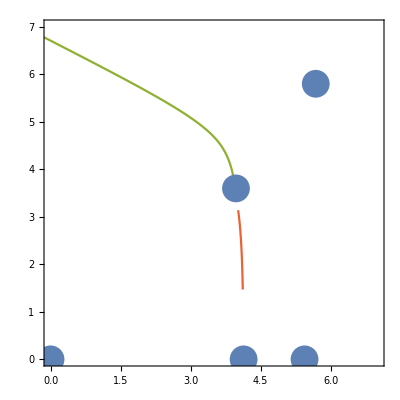
{-Graphics-,{{0,0},{-1.,{0.,1.}}
{-1.,{1.,0.}}}
{{3.97058,3.59652},{-0.344478,{-0.0102954,0.999947}}
{0.32445,{0.0472104,0.998885}}}
{{4.13427,0},{0.497354,{0.0248353,0.999692}}
{0.232617,{1.,0.}}}
{{5.43898,0},{1.56727,{0.00383553,0.999993}}
{-0.356052,{1.,0.}}}
{{5.67906,5.79816},{-1.59432,{-0.0121647,0.999926}}
{-0.547145,{-0.00853088,-0.999964}}}}

```mathematica
Module[{α12=4.849206349206349,α21=282.46153846153845,β11=132.92307692307693,β12=94.,λ1=3,λ2=2.666666666666667,μ2=1},Quiet[Module[{eq$,st$,diffs$,J$,es$,sep0$,ics$,sol$},eq$={x2 (1-1/2 ω (1+ω)+(ω c12)/(1+c12))+β11 x1-(c21+(α21 c21 x1)/(1+c21)),β12 (1-1/2 θ (1+θ)+(θ c21)/(1+c21)) x1-(c12+(α12 c12 x2)/(1+c12)),x1 ((λ1 c21 (1-x1))/(1+c21)-1),μ2 x2 ((λ2 c12)/(1+c12)-1)};st$=Sort/@NSolve[Join[Thread[eq$==0],{x1≥0,x2≥0,c12≥0,c21≥0}],{x1,x2,c12,c21}];diffs$=FullSimplify[Solve[Flatten[D[(Thread[eq$⟦1;;2⟧==0]/.v:c12|c21->v[x1,x2]), {{x1,x2}}]],{Derivative[0,1][c21][x1,x2],Derivative[0,1][c12][x1,x2],Derivative[1,0][c12][x1,x2],Derivative[1,0][c21][x1,x2]}]⟦1⟧]/.x_[x1,x2]->x;J$=FullSimplify[D[(eq$⟦3;;All⟧/.v:c12|c21->v[x1,x2]), {{x1,x2}}]]/.diffs$/.x_[x1,x2]->x;es$=({#1⟦3;;All⟧/.v:x1|x2->v[t],Transpose[Eigensystem[J$/.#1]]}&)/@st$;sep0$=({#1⟦1⟧,(1/10 {#1,-#1}&)[Select[#1⟦2⟧,Sign[#1⟦1⟧]==-1&]⟦1,2⟧]}&)/@Select[es$,Sign[Times@@#1⟦2,1;;All,1⟧]==-1&];ics$=(Transpose[{x1[t],x2[t]}+Transpose[#1⟦2⟧]]/.#1⟦1⟧&)/@sep0$;sol$[{x10$_,x20$_}]:=Module[{adeq$,steq$,event$},adeq$=Thread[{0,0,x1'[t],x2'[t]}==(eq$/.v:x1|x2|c12|c21->v[t])];steq$=Join[Apply[Equal,FindRoot[(#1==0&)/@eq$⟦1;;2⟧/.{v:c21|c12->v[0],x1->x10$,x2->x20$},{c12[0],1,0,∞},{c21[0],1,0,∞}],{1}],Thread[{x1[0],x2[0]}=={x10$,x20$}]];event$={WhenEvent[(x1[t]>8||x1[t]<0)||(x2[t]>8||x2[t]<0),"StopIntegration"]};NDSolveValue[Join[adeq$,steq$],{x1[t],x2[t]},{t,0,-10}]];{Show[{ParametricPlot[Evaluate[(#1+{6,Log10[(γ  k21)/β21]/.Thread[{k21,β21,γ}->{1.3*^9,100800,2}]}&)/@Log10[Flatten[Map[sol$,ics$,{2}],1]]],{t,-10,0}],ListPlot[(#1+{6,Log10[(γ k21)/β21]/.Thread[{k21,β21,γ}->{1.3*^9,100800,2}]}&)/@Log10[{x1,x2}/.st$]/.-∞->0,PlotStyle->PointSize[0.05]]},AspectRatio->1,Axes->False,Frame->True,PlotRange->{{0,7},{0,7}},PlotRangePadding->None],TableForm[({Log10[{x1[t],x2[t]}]+{6,Log10[(γ k21)/β21]/.Thread[{k21,β21,γ}->{1.3*^9,100800,2}]}/.#1⟦1⟧/.-∞->0,TableForm[#1⟦2⟧,TableDepth->1]}&)/@Sort[es$],TableDepth->1]}]]]
```

Figure S3:

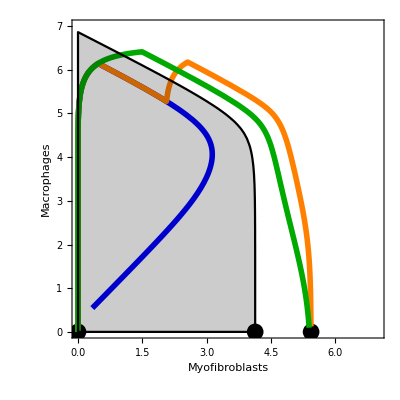

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800/100,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=1.8},Quiet@Show[
Graphics[{PointSize[0.03],Point[Log10[FP2[[;;,{4,1},2]]/.(0->1)]]}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,45},PlotStyle->{Thickness[0.01],Blue}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,67},PlotStyle->{Thickness[0.01],Darker[Green]}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,7}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

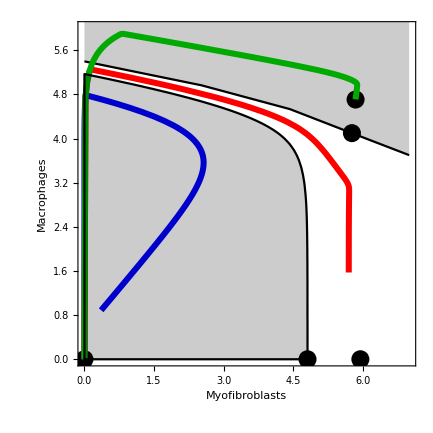

```mathematica
Module[{a=1,b=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=279.13846153846157(*1353600*),α21=39000.(*734400*),β11=11440(*345600*),β12=2520.(*676800*),β21=100800,γ=2,λ1=2.4(*0.9*),λ2=2.4(*0.8*),μ1=0.3,μ2=0.3,τ1=0.02,τ2=0.06,τ3=0.3},
Quiet@Show[
ListLinePlot[Join[pnts4,Log10[Re[FP3[[;;,{4,1},2]]]/.(0->1)][[{4}]],{{7,3.7}}],InterpolationOrder->1,Filling->7,PlotStyle->Black],
Graphics[{PointSize[0.03],Point[Log10[FP3[[;;,{4,1},2]]/.(0->1)]]}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,30},PlotStyle->{Thickness[0.01],Blue}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,200},PlotStyle->{Thickness[0.01],Red}],
ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ3,1,1,1,1,1}]⟦1;;2⟧)/.t->0.3t1]),{t1,0,200},PlotStyle->{Thickness[0.01],Darker[Green]}],
ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,-1,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
PlotRange->{{0,7},{0,6}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{"Myofibroblasts","Macrophages"}]]
```

Figure S4:

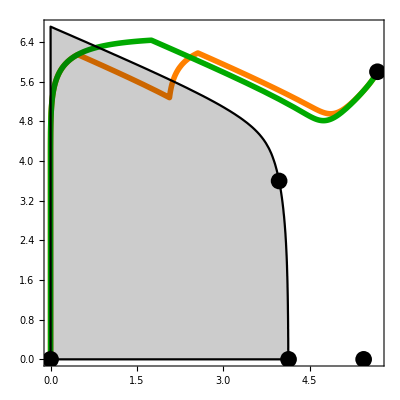

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=2.1},Show[ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),(*β21/(γ k21 μ1)*)I0,τ1,.1,1,1,1,1}]⟦1;;2⟧)]),{t,0,14},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],ParametricPlot[(Evaluate[{6,Log10@((β21/(γ k21))^-1)}+Log10@(admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),(*β21/(γ k21 μ1)*)I0,τ2,.1,1,1,1,1}]⟦1;;2⟧)]),{t,0,20},PlotStyle->{Thickness[0.01],Darker[Green]},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],ListLinePlot[
#[[1]][[#[[2,1]]]]&@Cases[
RegionPlot[
separatrix[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,10^(x01-6),β21/(k21 γ)10^x02}],
{x01,0,6},{x02,0,8}],
{{_Real,_Real}..}|Line[y_],∞],
PlotRange->{{0,8},{0,8}},AspectRatio->1,Axes->False,Frame->True,Filling->Axis,PlotStyle->Black],
Graphics[{PointSize[0.03],Point[Log10[FP[[;;,{4,1},2]]/.(0->1)]]}]]]//Quiet
```

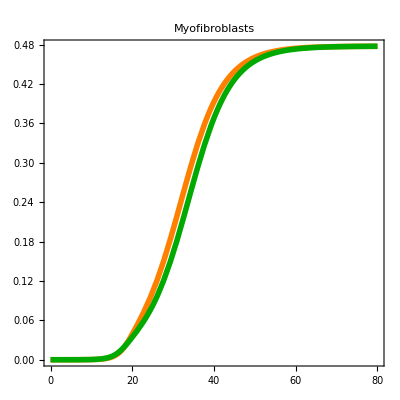
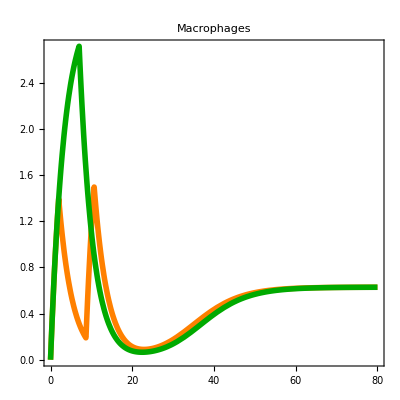
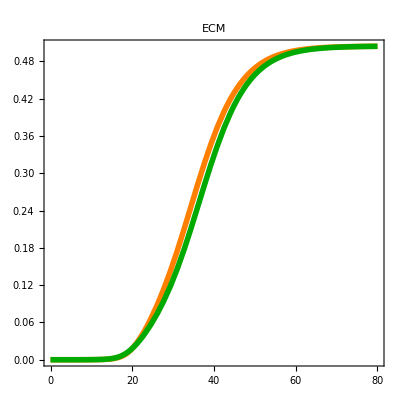

```mathematica
Module[{α=1,ϵ=0.1,a=1,b=1,c=1,I0=120,k12=3.6*^9,k21=1.3*^9,α12=1353600,α21=734400,β11=345600,β12=676800,β21=100800,γ=2,λ1=0.9,λ2=0.8,μ1=0.3,μ2=0.3,τ1=0.6,τ2=2.1},
Quiet@{Show[
Plot[(Evaluate[admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,α,ϵ,c,a,b}][[1]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker@Green},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],PlotLabel->"Myofibroblasts"],
Show[
Plot[(Evaluate[1/(10^6 β21/(γ k21))admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[1/(10^6 β21/(γ k21))admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,α,ϵ,c,a,b}][[2]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker@Green},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],PlotLabel->"Macrophages"],
Show[
Plot[(Evaluate[admodelRepet[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ1,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Orange},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],
Plot[(Evaluate[admodel[{0,0,(α21 10^6)/(γ k21),(α12 k21)/(β21 k12),(β12 10^6)/(γ k12),(β11 10^6)/(γ k21),μ2/μ1,λ1/μ1,λ2/μ2,1/10^6,1/(10^(Log10@((β21/(γ k21))^-1))),I0,τ2,α,ϵ,c,a,b}][[3]]/.t->0.3 t1]),{t1,0,80},PlotStyle->{Thickness[0.01],Darker@Green},PlotRange->All,AspectRatio->1,Axes->False,Frame->True],PlotLabel->"ECM"]}]
```